```mathematica
(* Mathematica*)
Clear[cr,cols,cr2,cr3,cr4,p,p0,q0,r0,s0,s,v]
allColors=ColorData["Legacy"][[3,1]];
firstCols={ "Cyan","ManganeseBlue","DodgerBlue" ,"Blue","Magenta","Purple","White","AliceBlue","LightBlue" ,"Cyan","ManganeseBlue","DodgerBlue" ,"Blue","Magenta","Purple","Pink","Tomato","Red","DarkOrange","Orange","DeepNaplesYellow","Gold","Banana","Yellow","LightYellow","Orange","Pink","LightPink","Yellow","LightYellow","LightPink","White","DeepNaplesYellow", "Orange","DarkOrange","Tomato","Red","Tomato","Pink","LightPink","DeepNaplesYellow", "Orange","DarkOrange","Tomato","White","Pink","Banana","LightBlue","DodgerBlue","Cyan","White","Purple","DarkOrchid","Magenta","ManganeseBlue","DeepNaplesYellow", "Orange","DarkOrange","Tomato","GoldOchre","LightPink","Magenta","Green","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","Yellow","Tomato","DeepNaplesYellow","DodgerBlue","Cyan","Red","Blue","DeepNaplesYellow","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","LimeGreen"};
cols=ColorData["Legacy",#]&/@Join[firstCols,Complement[allColors,firstCols]];
rotate[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
cr[n_]:=cr[n]=cols[[n]];
cr2[n_]:=cr2[n]=cols[[n+8]];
cr3[n_]:=cr3[n]=cols[[n+16]];
cr4[n_]:=cr4[n]=cols[[n+24]];
cr5[n_]:=cr5[n]=cols[[n+36]]
```

```mathematica
cr5[n_]:=cr5[n]=cols[[n+16]]
```

```mathematica
(*Mathematica *)
```

```mathematica
(* D_8  45 degree as Goldman 4 puncture solved A.B.C.D={{1,0},{0,1}}*)
```

```mathematica
w=Exp[2*Pi*I/8]
```

ⅇ^((ⅈ π)/4)

```mathematica
s[1]=N[{{w,Sqrt[8]},{0,1/w}}]
s[2]={{0,1},{1,0}}.s[1]
s[3]=N[{{w,0},{Sqrt[8],1/w}}]
```

{{0.707107+0.707107 ⅈ,2.82843},{0.,0.707107-0.707107 ⅈ}}

{{0.+0. ⅈ,0.707107-0.707107 ⅈ},{0.707107+0.707107 ⅈ,2.82843+0. ⅈ}}

{{0.707107+0.707107 ⅈ,0.},{2.82843,0.707107-0.707107 ⅈ}}

```mathematica
m=s[1].s[2].s[3].{{a0,b0},{c0,d0}}-{{1,0},{0,1}}
```

{{-1+(25.4558+2.82843 ⅈ) a0+(6.36396-6.36396 ⅈ) c0,(25.4558+2.82843 ⅈ) b0+(6.36396-6.36396 ⅈ) d0},{(6.36396-4.94975 ⅈ) a0+(4.44089×10^-16-2.82843 ⅈ) c0,-1+(6.36396-4.94975 ⅈ) b0+(4.44089×10^-16-2.82843 ⅈ) d0}}

```mathematica
s[4]=Flatten[{{a0,b0},{c0,d0}}/.Solve[Flatten[Table[m[[i,j]]==0,{i,2},{j,2}],1],{a0,b0,c0,d0}]//Chop,1]
```

{{0.+2.82843 ⅈ,6.36396-6.36396 ⅈ},{6.36396-4.94975 ⅈ,-25.4558-2.82843 ⅈ}}

```mathematica
(* first Maloni gluing of {A,B} punctures to give E*)
```

```mathematica
om0=s[1]
```

{{0.707107+0.707107 ⅈ,2.82843},{0.,0.707107-0.707107 ⅈ}}

```mathematica
om1=s[2]
```

{{0.+0. ⅈ,0.707107-0.707107 ⅈ},{0.707107+0.707107 ⅈ,2.82843+0. ⅈ}}

```mathematica
J={{-I,0},{0,I}}
```

{{-ⅈ,0},{0,ⅈ}}

```mathematica
tau=N[Exp[I*Pi/2]]
```

0.+1. ⅈ

```mathematica
T={{1,tau},{0,1}}
```

{{1,0.+1. ⅈ},{0,1}}

```mathematica
glu1=Inverse[om1].Inverse[J].Inverse[T].om0
```

{{2.-2. ⅈ,-3.-6. ⅈ},{-1.+2.22045×10^-16 ⅈ,-1.+2. ⅈ}}

```mathematica
(* Second Maloni gluing of {C,D} punctures to give F*)
```

```mathematica
om0=s[3]
```

{{0.707107+0.707107 ⅈ,0.},{2.82843,0.707107-0.707107 ⅈ}}

```mathematica
om1=s[4]
```

{{0.+2.82843 ⅈ,6.36396-6.36396 ⅈ},{6.36396-4.94975 ⅈ,-25.4558-2.82843 ⅈ}}

```mathematica
J={{-I,0},{0,I}}
```

{{-ⅈ,0},{0,ⅈ}}

```mathematica
tau=N[Exp[I*Pi/2]]
```

0.+1. ⅈ

```mathematica
T={{1,tau},{0,1}}
```

{{1,0.+1. ⅈ},{0,1}}

```mathematica
glu2=Inverse[om1].Inverse[J].Inverse[T].om0
```

{{34.+6. ⅈ,11.-16. ⅈ},{9.-6. ⅈ,-1.-6. ⅈ}}

```mathematica
s[5]=glu1
s[6]=glu2
```

{{2.-2. ⅈ,-3.-6. ⅈ},{-1.+2.22045×10^-16 ⅈ,-1.+2. ⅈ}}

{{34.+6. ⅈ,11.-16. ⅈ},{9.-6. ⅈ,-1.-6. ⅈ}}

```mathematica
(* Third Maloni gluing of {E,F} genus 2 to get G*)
```

```mathematica
om0=s[5]
```

{{2.-2. ⅈ,-3.-6. ⅈ},{-1.+2.22045×10^-16 ⅈ,-1.+2. ⅈ}}

```mathematica
om1=s[6]
```

{{34.+6. ⅈ,11.-16. ⅈ},{9.-6. ⅈ,-1.-6. ⅈ}}

```mathematica
J={{-I,0},{0,I}}
```

{{-ⅈ,0},{0,ⅈ}}

```mathematica
tau=N[Exp[I*Pi/2]]
```

0.+1. ⅈ

```mathematica
T={{1,tau},{0,1}}
```

{{1,0.+1. ⅈ},{0,1}}

```mathematica
glu3=Inverse[om1].Inverse[J].Inverse[T].om0
```

{{5.+19. ⅈ,49.+8. ⅈ},{27.-22. ⅈ,-23.-85. ⅈ}}

```mathematica
s[7]=glu3
```

{{5.+19. ⅈ,49.+8. ⅈ},{27.-22. ⅈ,-23.-85. ⅈ}}

```mathematica
(* D_8  45 degree as T(0,3) solved A.B.C.D.E.F.G.H={{1,0},{0,1}}*)
```

```mathematica
m1=s[1].s[2].s[3].s[4].s[5].s[6].s[7].{{a1,b1},{c1,d1}}-{{1,0},{0,1}}
```

{{-1+(12.-1. ⅈ) a1+(8.-27. ⅈ) c1,(12.-1. ⅈ) b1+(8.-27. ⅈ) d1},{(-3.-3. ⅈ) a1-(9.-4. ⅈ) c1,-1-(3.+3. ⅈ) b1-(9.-4. ⅈ) d1}}

```mathematica
s[8]=Flatten[{{a1,b1},{c1,d1}}/.Solve[Flatten[Table[m1[[i,j]]==0,{i,2},{j,2}],1],{a1,b1,c1,d1}]//Chop,1]
```

{{-9.+4. ⅈ,-8.+27. ⅈ},{3.+3. ⅈ,12.-1. ⅈ}}

```mathematica
Table[Det[s[i]],{i,8}]//Chop

Table[Tr[s[i]],{i,8}]//Chop
Sum[s[i].s[i],{i,8}]//Chop
```

{1.,-1.,1.,-1.,-1.,-1.,1.,1.}

{1.41421,2.82843,1.41421,-25.4558,1.,33.,-18.-66. ⅈ,3.+3. ⅈ}

{{2251.-561. ⅈ,-255.-3695. ⅈ},{-1798.-1438. ⅈ,-4533.+2955. ⅈ}}

```mathematica
(* the Möbius transforms : Kleinian group in SL(2,c)*)
```

```mathematica
s0=N[{{1,-I},{-I,1}}/Sqrt[2]];s1=Inverse[s0];
qf=N[rotate[Pi/4]];qfi=Inverse[qf];
{a,b,c,d,A0,B0,C0,D0}=Table[N[qf.s[i].qfi],{i,8}]
```

{{{-0.707107+0. ⅈ,1.41421+0.707107 ⅈ},{-1.41421+0.707107 ⅈ,2.12132+0. ⅈ}},{{0.707107+0. ⅈ,-1.41421-0.707107 ⅈ},{-1.41421+0.707107 ⅈ,2.12132+0. ⅈ}},{{-0.707107+0. ⅈ,-1.41421+0.707107 ⅈ},{1.41421+0.707107 ⅈ,2.12132+0. ⅈ}},{{-19.0919+5.65685 ⅈ,12.7279+2.12132 ⅈ},{12.7279+3.53553 ⅈ,-6.36396-5.65685 ⅈ}},{{2.5+3. ⅈ,0.5-5. ⅈ},{2.5+1. ⅈ,-1.5-3. ⅈ}},{{6.5+11. ⅈ,18.5+1. ⅈ},{16.5+11. ⅈ,26.5-11. ⅈ}},{{-47.-26. ⅈ,25.+67. ⅈ},{3.+37. ⅈ,29.-40. ⅈ}},{{4.-13.5 ⅈ,-16.+14.5 ⅈ},{-5.-9.5 ⅈ,-1.+16.5 ⅈ}}}

```mathematica
Det[a]
Tr[a]
Det[b]
Tr[b]
Det[A0]
Tr[A0]
Det[B0]
Tr[B0]
Affine[{z1_,z2_}]:=0.00001 Round[(z1/z2)/0.00001];
Children[{z_,n_}]:={Affine[{a,b,c,d,A0,B0,C0,D0}[[#]].{z,1}],#}&/@Delete[Range[8],{5,6,7,8,1,2,3,4}[[n]]];
aa1={Re[#[[1]]],Im[#[[1]]]}&/@Nest[Union[Flatten[Children/@#,1]]&,ParallelTable[{Affine[{a,b,c,d,A0,B0,C0,D0}[[i]].{0,1}],i},{i,1,8}],8];
ll=Length[aa1]
Last[aa1]
aa=Delete[Union[aa1],Length[Union[aa1]]];
```

1.+0. ⅈ

1.41421+0. ⅈ

-1.+0. ⅈ

2.82843+0. ⅈ

-1.+2.498×10^-15 ⅈ

1.+4.44089×10^-16 ⅈ

-1.+2.79429×10^-14 ⅈ

33.-1.50457×10^-12 ⅈ

1185292

{2.54762×10^15,5.09524×10^15}

```mathematica
g0=Rasterize[ListPlot[aa,AspectRatio->Automatic,ColorFunction->"DarkRainbow",PlotStyle->{PointSize[0.001]},ImageSize->2000,PlotRange->{{-4,4},{-4,4}}*3/4],RasterSize->2000,ImageSize->2000];
```

```mathematica
dlst=ParallelTable[Mod[1+Floor[1+(1+Floor[18*Norm[aa[[i]]]])/(Abs[Cos[Arg[aa[[i,1]]+I*aa[[i,2]]]]]+Abs[Sin[Arg[aa[[i,1]]+I*aa[[i,2]]]]])],Length[cols]],{i,Length[aa]}];
Min[dlst];
Max[dlst];
ptlst=Point[Developer`ToPackedArray[aa],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

```mathematica
g2=Rasterize[Graphics[{PointSize[.001],ptlst},AspectRatio->Automatic,ImageSize->2000,PlotRange->{{-4,4},{-4,4}}*3/4,Background->Black],RasterSize->2000,ImageSize->2000];
```

```mathematica
(* end limit set*)
```

```mathematica
(* Half plane to disk conformal map*)

bb1=Delete[Union[ParallelTable[{-(Im[-1/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,1⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,2⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]+2 Re[aa⟦i,2⟧/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]),-2 Im[aa⟦i,2⟧/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]+Re[-1/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,1⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,2⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]},{i,Length[aa]}]],Length[aa]];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
(*ListPlot[bb1,PlotStyle->{{Magenta,PointSize[0.001]},{Purple,PointSize[0.001]}},ImageSize->1000,Axes->True,PlotRange->All]*)
```

```mathematica
ptlst3:=Point[Developer`ToPackedArray[bb1],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

```mathematica
g3=Rasterize[Graphics[{PointSize[.001],ptlst3(*,ptlst2*)},AspectRatio->Automatic,ImageSize->2000,Background->Black,PlotRange->{{-1.1,1.1},{-1.1,1.1}}*7],RasterSize->2000,ImageSize->2000];
```

```mathematica
(* Sphere conformal map*)

cc1=ParallelTable[{2*aa[[i,1]],2*aa[[i,2]],(1-aa[[i]].aa[[i]])}/(1+aa[[i]].aa[[i]]),{i,Length[aa]}];
```

```mathematica
ptlst5a=Point[Developer`ToPackedArray[cc1],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

```mathematica
g4=Rasterize[Graphics3D[{PointSize[.001],ptlst5a},AspectRatio->Automatic,ImageSize->2000,PlotRange->All,Background->Black,Boxed->False],RasterSize->2000,ImageSize->2000];
```

```mathematica
Export["Nylander_8group_D_8_Goldman_Maloni_T30_scaleSqrt8_Quasiconformal45_8Limitset_8.jpg",{g0,g2,g3,g4}]
```

Nylander_8group_D_8_Goldman_Maloni_T30_scaleSqrt8_Quasiconformal45_8Limitset_8.jpg

```mathematica
(*end*)
```

```mathematica
(*mathematica*)
```

```mathematica
(*2Nylander_8group_D_8_Goldman_Maloni_T30_scaleSqrt8_8Limitset_8_crop.jpg;
-Graphics-*)
```

```mathematica
s={{{-0.7071067811865477+0. ⅈ,1.4142135623730951+0.7071067811865475 ⅈ},{-1.4142135623730951+0.7071067811865475 ⅈ,2.121320343559643+0. ⅈ}},{{0.7071067811865477+0. ⅈ,-1.4142135623730951-0.7071067811865475 ⅈ},{-1.4142135623730951+0.7071067811865475 ⅈ,2.121320343559643+0. ⅈ}},{{-0.7071067811865477+0. ⅈ,-1.4142135623730951+0.7071067811865475 ⅈ},{1.4142135623730951+0.7071067811865475 ⅈ,2.121320343559643+0. ⅈ}},{{-19.091883092036785+5.656854249492266 ⅈ,12.727922061357837+2.1213203435597117 ⅈ},{12.727922061357829+3.5355339059328044 ⅈ,-6.363961030678881-5.656854249492409 ⅈ}},{{2.5+3.000000000000001 ⅈ,0.4999999999999998-5.000000000000001 ⅈ},{2.5000000000000004+1.0000000000000004 ⅈ,-1.5000000000000004-3.0000000000000004 ⅈ}},{{6.499999999997756+10.999999999995016 ⅈ,18.499999999992195+0.999999999998697 ⅈ},{16.499999999993502+10.999999999994591 ⅈ,26.499999999988265-10.99999999999652 ⅈ}},{{-46.999999999998984-25.99999999999777 ⅈ,25.00000000000093+66.99999999999687 ⅈ},{3.000000000000858+36.99999999999858 ⅈ,28.999999999997883-39.99999999999932 ⅈ}},{{4.000000000002976-13.499999999998986 ⅈ,-15.999999999995303+14.499999999992765 ⅈ},{-4.99999999999817-9.500000000000913 ⅈ,-1.000000000000759+16.499999999993616 ⅈ}}}
```

{{{-0.707107+0. ⅈ,1.41421+0.707107 ⅈ},{-1.41421+0.707107 ⅈ,2.12132+0. ⅈ}},{{0.707107+0. ⅈ,-1.41421-0.707107 ⅈ},{-1.41421+0.707107 ⅈ,2.12132+0. ⅈ}},{{-0.707107+0. ⅈ,-1.41421+0.707107 ⅈ},{1.41421+0.707107 ⅈ,2.12132+0. ⅈ}},{{-19.0919+5.65685 ⅈ,12.7279+2.12132 ⅈ},{12.7279+3.53553 ⅈ,-6.36396-5.65685 ⅈ}},{{2.5+3. ⅈ,0.5-5. ⅈ},{2.5+1. ⅈ,-1.5-3. ⅈ}},{{6.5+11. ⅈ,18.5+1. ⅈ},{16.5+11. ⅈ,26.5-11. ⅈ}},{{-47.-26. ⅈ,25.+67. ⅈ},{3.+37. ⅈ,29.-40. ⅈ}},{{4.-13.5 ⅈ,-16.+14.5 ⅈ},{-5.-9.5 ⅈ,-1.+16.5 ⅈ}}}

```mathematica
ss=Table[(s[[i,1,1]]*x+s[[i,1,2]])/(s[[i,1,1]]*x+s[[i,2,2]]),{i,Length[s]}]
```

{((1.41421+0.707107 ⅈ)-(0.707107+0. ⅈ) x)/((2.12132+0. ⅈ)-(0.707107+0. ⅈ) x),((-1.41421-0.707107 ⅈ)+(0.707107+0. ⅈ) x)/((2.12132+0. ⅈ)+(0.707107+0. ⅈ) x),((-1.41421+0.707107 ⅈ)-(0.707107+0. ⅈ) x)/((2.12132+0. ⅈ)-(0.707107+0. ⅈ) x),((12.7279+2.12132 ⅈ)-(19.0919-5.65685 ⅈ) x)/((-6.36396-5.65685 ⅈ)-(19.0919-5.65685 ⅈ) x),((0.5-5. ⅈ)+(2.5+3. ⅈ) x)/((-1.5-3. ⅈ)+(2.5+3. ⅈ) x),((18.5+1. ⅈ)+(6.5+11. ⅈ) x)/((26.5-11. ⅈ)+(6.5+11. ⅈ) x),((25.+67. ⅈ)-(47.+26. ⅈ) x)/((29.-40. ⅈ)-(47.+26. ⅈ) x),((-16.+14.5 ⅈ)+(4.-13.5 ⅈ) x)/((-1.+16.5 ⅈ)+(4.-13.5 ⅈ) x)}

```mathematica
p0[x_]=Together[FullSimplify[ExpandAll[Product[ss[[i]],{i,Length[ss]}]]]]
```

((5.55112×10^-17+1. ⅈ) ((25.2889+11.0585 ⅈ)-(113.552-47.6955 ⅈ) x+(56.0731-227.816 ⅈ) x^2+(188.167+184.144 ⅈ) x^3-(186.828-62.6171 ⅈ) x^4+(11.1253-100.094 ⅈ) x^5+(31.4266+17.3829 ⅈ) x^6-(7.07168-5.00156 ⅈ) x^7-(0.+1. ⅈ) x^8))/((6.88243+23.0419 ⅈ)+(50.961-43.6342 ⅈ) x-(134.971+5.61094 ⅈ) x^2+(107.207+69.8409 ⅈ) x^3-(51.6792+43.3961 ⅈ) x^4+(28.428+0.692401 ⅈ) x^5-(1.601-4.85945 ⅈ) x^6-(4.55212+0.879312 ⅈ) x^7+1. x^8)

```mathematica
p[x_]=Denominator[p0[x]]
```

(6.88243+23.0419 ⅈ)+(50.961-43.6342 ⅈ) x-(134.971+5.61094 ⅈ) x^2+(107.207+69.8409 ⅈ) x^3-(51.6792+43.3961 ⅈ) x^4+(28.428+0.692401 ⅈ) x^5-(1.601-4.85945 ⅈ) x^6-(4.55212+0.879312 ⅈ) x^7+1. x^8

```mathematica
q[x_]=Numerator[p0[x]]//Chop
```

(0.+1. ⅈ) ((25.2889+11.0585 ⅈ)-(113.552-47.6955 ⅈ) x+(56.0731-227.816 ⅈ) x^2+(188.167+184.144 ⅈ) x^3-(186.828-62.6171 ⅈ) x^4+(11.1253-100.094 ⅈ) x^5+(31.4266+17.3829 ⅈ) x^6-(7.07168-5.00156 ⅈ) x^7-(0.+1. ⅈ) x^8)

```mathematica
(* Mathematica*)
<<ComputationalGeometry`
```

```mathematica
pa[x_]=p[x]
```

(6.88243+23.0419 ⅈ)+(50.961-43.6342 ⅈ) x-(134.971+5.61094 ⅈ) x^2+(107.207+69.8409 ⅈ) x^3-(51.6792+43.3961 ⅈ) x^4+(28.428+0.692401 ⅈ) x^5-(1.601-4.85945 ⅈ) x^6-(4.55212+0.879312 ⅈ) x^7+1. x^8

```mathematica
a0={Re[x],Im[x]}/.NSolve[pa[x]==0,x]
```

{{-3.,0},{-0.313936,2.22358},{-0.225725,-0.363178},{0.111958,-0.912998},{0.836066,0.196721},{1.14376,-0.264817},{3.,0},{3.,0}}

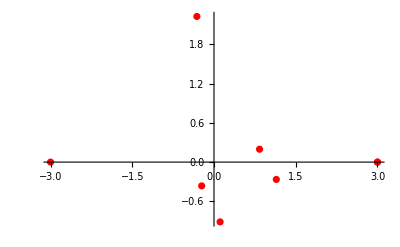

```mathematica
ListPlot[a0,PlotStyle->Red,PlotRange->All]
```

```mathematica
Length[a0]
```

8

```mathematica
pts=Union[{2*Re[x],2*Im[x],1-Abs[x]^2}/(1+Abs[x]^2)/.NSolve[pa[x]==0,x]]//Chop
```

{{-0.6,0,-0.8},{-0.381663,-0.614072,0.690832},{-0.103903,0.735935,-0.669032},{0.121292,-0.98911,0.0833646},{0.6,0,-0.8},{0.961824,-0.222694,-0.159067},{0.962264,0.226415,0.150943}}

```mathematica
ptsn=Table[Hue[Norm[x/.NSolve[pa[x]==0,x][[i]]]/1.75],{i,Length[pts]}]
```

{Hue[1.7142857142857137],Hue[1.283220313838411],Hue[0.24434832076498622],Hue[0.5256212712530668],Hue[0.49079857226903045],Hue[0.6708654694968184],Hue[1.7142857142857184]}

```mathematica
(* Voronoi diagram*)
```

```mathematica
a=Union[Most/@pts];
```

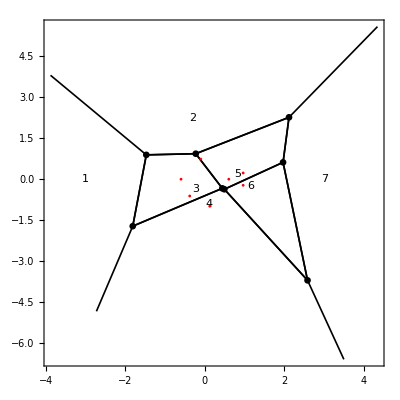

```mathematica
g1=Show[{
DiagramPlot[a0],
Graphics[{Red,PointSize[.005],Point[a]}]
},PlotRange->All,Frame->True,ImageSize->Full]
```

```mathematica
g2=Show[Graphics3D[{Red,PointSize[0.0375/3],Point/@pts}],Axes->True,ImageSize->1000,ViewPoint->{5,5,5}];
```

```mathematica
(*(* Voronoi diagram*)
g1=Show[{
DiagramPlot[a0,LabelPoints->False]/._Point:>{},
Graphics[{Red,PointSize[.005],Point[a0]}]
},PlotRange->All,Frame->True,PlotRangeClipping->True,ImageSize->1000]
(* 3d projection of polyhedron*)*)
```

```mathematica
(* convex hull: MathWorld Library*)
<<ConvexHull`
```

```mathematica
hull0=ConvexHull3D[pts]
```

{Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…]}

```mathematica
ga=Show[Graphics3D[ConvexHull3D[pts]]];
```

```mathematica
Length[hull0]
```

10

```mathematica
gb=hull1=Show[Graphics3D[Flatten[Table[If[i≤Length[ptsn],{ptsn[[i]],hull0[[i]]},{}],{i,Length[hull0]}]]]];
```

```mathematica
hull3=Show[{ga,gb},ViewPoint->{3,3,3},ImageSize->2000,ViewPoint->{2,2,2}];
```

```mathematica
Export["8 group_D _ 8 _Goldman _Maloni _T30 _scaleSqrt8_Quasiconformal_45Convex_Hull.jpg",hull3]
(*end*)
```

8 group_D _ 8 _Goldman _Maloni _T30 _scaleSqrt8_Quasiconformal_45Convex_Hull.jpg

```mathematica
(*Mathematica*)
```

```mathematica
(*Heman rings Julia*)
```

```mathematica
f[x_]=Exp[2*Pi*I/GoldenRatio]*x^2*((5.551115123125783*^-17+0.9999999999999998 ⅈ) ((25.288865734119458+11.058481151353709 ⅈ)-(113.55200560684268-47.69554293018427 ⅈ) x+(56.073106328527714-227.81560648925787 ⅈ) x^2+(188.1674425147408+184.1435628344996 ⅈ) x^3-(186.82768341901675-62.61708359294152 ⅈ) x^4+(11.12534242603561-100.093627960257 ⅈ) x^5+(31.426592048481027+17.38290379968851 ⅈ) x^6-(7.071681603717327-5.00156168133099 ⅈ) x^7-(0.+1. ⅈ) x^8))/((6.88242921244526+23.041945597540018 ⅈ)+(50.96095526973619-43.634153228243136 ⅈ) x-(134.97138997345965+5.610936413747244 ⅈ) x^2+(107.20722261346319+69.84087019905272 ⅈ) x^3-(51.67915830375064+43.3960730427611 ⅈ) x^4+(28.428028542938655+0.6924005079169377 ⅈ) x^5-(1.6009987611076864-4.85944910643324 ⅈ) x^6-(4.552121084731056+0.8793115496632422 ⅈ) x^7+1. x^8)//Chop
```

((0.67549-0.737369 ⅈ) x^2 ((25.2889+11.0585 ⅈ)-(113.552-47.6955 ⅈ) x+(56.0731-227.816 ⅈ) x^2+(188.167+184.144 ⅈ) x^3-(186.828-62.6171 ⅈ) x^4+(11.1253-100.094 ⅈ) x^5+(31.4266+17.3829 ⅈ) x^6-(7.07168-5.00156 ⅈ) x^7-(0.+1. ⅈ) x^8))/((6.88243+23.0419 ⅈ)+(50.961-43.6342 ⅈ) x-(134.971+5.61094 ⅈ) x^2+(107.207+69.8409 ⅈ) x^3-(51.6792+43.3961 ⅈ) x^4+(28.428+0.692401 ⅈ) x^5-(1.601-4.85945 ⅈ) x^6-(4.55212+0.879312 ⅈ) x^7+1. x^8)

```mathematica
(*g0=JuliaSetPlot[f[z],z,ColorFunction->"CMYKColors",ImageResolution->2000,ImageSize->2000]*)
```

#### 3D Mandelbrot

```mathematica
(*Julia with SQRT(x^2+y^2) limited measure*)
(*by R. L. BAGULA 17 Apr 2023 © *)
numberOfz2ToEscape[z_] := Block[
	{escapeCount, nz = N[z],nzold=0},
	For[
		escapeCount = 0,
		(Sqrt[Re[nz]^2+Im[nz]^2] <128) && (escapeCount <2048) && (Abs[nz-nzold]>10^(-3)),
		nzold=nz;
		nz=f[nz];
		++escapeCount
	];
	escapeCount*If[(Abs[nz-nzold]>10^(-3))||escapeCount>2000,escapeCount*Abs[Arg[nz]],escapeCount*Abs[ArcTan[nz]+I*ArcTan[nz]*Tan[1]-Arg[z]]]
]
```

```mathematica
FractalPure[m_][{{ReMin_, ReMax_, ReSteps_},
			 {ImMin_, ImMax_, ImSteps_}}] :=
		ParallelTable[
			numberOfz2ToEscape[x + y I],
			{y, ImMin, ImMax, (ImMax - ImMin)/ImSteps},
			{x, ReMin, ReMax, (ReMax - ReMin)/ReSteps}
		
	]
```

```mathematica
arraym=FractalPure[m][{{-4.,4.,1000},{-2.5,5.5,1000}}];
```

```mathematica
g1=ListPlot3D[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False,AspectRatio -> Automatic,Boxed->False, Axes->False,ColorFunction->"Rainbow",Background->Black,ViewPoint->Above,ImageSize->2000];
```

```mathematica
g2=ListDensityPlot[Log[Abs[1/Max[arraym]+arraym-512/(arraym+Max[arraym])]],
                          Mesh -> False,
		                  AspectRatio -> Automatic,
		                 ColorFunction->"GreenPinkTones",ImageSize->2000,Frame->False];
```

```mathematica
colortab=Reverse[Union[{{0,0,0.1875},{0,0,0.20833333333333331},{0,0,0.22916666666666666},{0,0,0.25},{0,0,0.2708333333333333},{0,0,0.28125},{0,0,0.29166666666666663},{0,0,0.3125},{0,0,1/3},{0,0,0.34375},{0,0,0.375},{0,0,0.40625},{0,0,0.4375},{0,0,0.46875},{0,0,1/2},{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.020833333333333332,1/3},{0,0.03125,1/2},{0,0.041666666666666664,1/3},{0,0.0625,1/3},{0,0.0625,1/2},{0,0.0625,1},{0,0.08333333333333333,1/3},{0,0.09375,1/2},{0,0.10416666666666666,1/3},{0,0.125,1/3},{0,0.125,1/2},{0,0.125,1},{0,0.14583333333333331,1/3},{0,0.15625,1/2},{0,0.16666666666666666,1/3},{0,0.1875,1/3},{0,0.1875,1/2},{0,0.1875,1},{0,0.20833333333333331,1/3},{0,0.21875,1/2},{0,0.22916666666666666,1/3},{0,0.25,1/3},{0,0.25,1/2},{0,0.25,1},{0,0.2708333333333333,1/3},{0,0.28125,1/2},{0,0.29166666666666663,1/3},{0,0.3125,1/3},{0,0.3125,1/2},{0,0.3125,1},{0,1/3,1/3},{0,0.34375,1/2},{0,0.375,1/2},{0,0.375,1},{0,0.40625,1/2},{0,0.4375,1/2},{0,0.4375,1},{0,0.46875,1/2},{0,0.5,1},{0,1/2,1/2},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.,0.,0.375},{0.,0.,0.41666666666666663},{0.,0.,0.4583333333333333},{0.,0.,0.5},{0.,0.,0.5416666666666666},{0.,0.,0.5833333333333333},{0.,0.,0.625},{0.,0.,0.6666666666666666},{0.,0.041666666666666664,0.6666666666666666},{0.,0.08333333333333333,0.6666666666666666},{0.,0.125,0.6666666666666666},{0.,0.16666666666666666,0.6666666666666666},{0.,0.20833333333333331,0.6666666666666666},{0.,0.25,0.6666666666666666},{0.,0.29166666666666663,0.6666666666666666},{0.,0.3333333333333333,0.6666666666666666},{0.,0.375,0.6666666666666666},{0.,0.41666666666666663,0.6666666666666666},{0.,0.4583333333333333,0.6666666666666666},{0.,0.5,0.6666666666666666},{0.,0.5416666666666666,0.6666666666666666},{0.,0.5833333333333333,0.6666666666666666},{0.,0.625,0.6666666666666666},{0.,0.6666666666666666,0.6666666666666666},{0.020833333333333332,1/3,1/3},{0.03125,1/2,1/2},{0.041666666666666664,1/3,0.3125},{0.041666666666666664,0.6666666666666666,0.6666666666666666},{0.0625,1/3,0.29166666666666663},{0.0625,1/2,0.46875},{0.0625,1,1},{0.08333333333333333,1/3,0.2708333333333333},{0.08333333333333333,0.6666666666666666,0.625},{0.09375,1/2,0.4375},{0.10416666666666666,1/3,0.25},{0.125,1/3,0.22916666666666666},{0.125,1/2,0.40625},{0.125,0.6666666666666666,0.5833333333333333},{0.125,1,0.9375},{0.14583333333333331,1/3,0.20833333333333331},{0.15625,1/2,0.375},{0.16666666666666666,1/3,0.1875},{0.16666666666666666,0.6666666666666666,0.5416666666666666},{0.1875,0,0},{0.1875,1/3,0.16666666666666666},{0.1875,1/2,0.34375},{0.1875,1,0.875},{0.20833333333333331,0,0},{0.20833333333333331,1/3,0.14583333333333331},{0.20833333333333331,0.6666666666666666,0.5},{0.21875,1/2,0.3125},{0.22916666666666666,0,0},{0.22916666666666666,1/3,0.125},{0.25,0,0},{0.25,1/3,0.10416666666666666},{0.25,1/2,0.28125},{0.25,0.6666666666666666,0.4583333333333333},{0.25,1,0.8125},{0.2708333333333333,0,0},{0.2708333333333333,1/3,0.08333333333333333},{0.28125,0,0},{0.28125,1/2,0.25},{0.29166666666666663,0,0},{0.29166666666666663,1/3,0.0625},{0.29166666666666663,0.6666666666666666,0.41666666666666663},{0.3125,0,0},{0.3125,1/3,0.041666666666666664},{0.3125,1/2,0.21875},{0.3125,1,0.75},{0.3333333333333333,0.6666666666666666,0.375},{1/3,0,0},{1/3,0.020833333333333332,0},{1/3,0.041666666666666664,0},{1/3,0.0625,0},{1/3,0.08333333333333333,0},{1/3,0.10416666666666666,0},{1/3,0.125,0},{1/3,0.14583333333333331,0},{1/3,0.16666666666666666,0},{1/3,0.1875,0},{1/3,0.20833333333333331,0},{1/3,0.22916666666666666,0},{1/3,0.25,0},{1/3,0.2708333333333333,0},{1/3,0.29166666666666663,0},{1/3,0.3125,0},{1/3,1/3,0},{1/3,1/3,0.020833333333333332},{0.34375,0,0},{0.34375,1/2,0.1875},{0.375,0,0},{0.375,0.,0.},{0.375,1/2,0.15625},{0.375,0.6666666666666666,0.3333333333333333},{0.375,1,0.6875},{0.40625,0,0},{0.40625,1/2,0.125},{0.41666666666666663,0.,0.},{0.41666666666666663,0.6666666666666666,0.29166666666666663},{0.4375,0,0},{0.4375,1/2,0.09375},{0.4375,1,0.625},{0.4583333333333333,0.,0.},{0.4583333333333333,0.6666666666666666,0.25},{0.46875,0,0},{0.46875,1/2,0.0625},{0.5,0.,0.},{0.5,0.6666666666666666,0.20833333333333331},{0.5,1,0.5625},{1/2,0,0},{1/2,0.03125,0},{1/2,0.0625,0},{1/2,0.09375,0},{1/2,0.125,0},{1/2,0.15625,0},{1/2,0.1875,0},{1/2,0.21875,0},{1/2,0.25,0},{1/2,0.28125,0},{1/2,0.3125,0},{1/2,0.34375,0},{1/2,0.375,0},{1/2,0.40625,0},{1/2,0.4375,0},{1/2,0.46875,0},{1/2,1/2,0},{1/2,1/2,0.03125},{0.5416666666666666,0.,0.},{0.5416666666666666,0.6666666666666666,0.16666666666666666},{0.5625,0,0},{0.5625,1,0.5},{0.5833333333333333,0.,0.},{0.5833333333333333,0.6666666666666666,0.125},{0.625,0,0},{0.625,0.,0.},{0.625,0.6666666666666666,0.08333333333333333},{0.625,1,0.4375},{0.6666666666666666,0.,0.},{0.6666666666666666,0.041666666666666664,0.},{0.6666666666666666,0.08333333333333333,0.},{0.6666666666666666,0.125,0.},{0.6666666666666666,0.16666666666666666,0.},{0.6666666666666666,0.20833333333333331,0.},{0.6666666666666666,0.25,0.},{0.6666666666666666,0.29166666666666663,0.},{0.6666666666666666,0.3333333333333333,0.},{0.6666666666666666,0.375,0.},{0.6666666666666666,0.41666666666666663,0.},{0.6666666666666666,0.4583333333333333,0.},{0.6666666666666666,0.5,0.},{0.6666666666666666,0.5416666666666666,0.},{0.6666666666666666,0.5833333333333333,0.},{0.6666666666666666,0.625,0.},{0.6666666666666666,0.6666666666666666,0.},{0.6666666666666666,0.6666666666666666,0.041666666666666664},{0.6875,0,0},{0.6875,1,0.375},{0.75,0,0},{0.75,1,0.3125},{0.8125,0,0},{0.8125,1,0.25},{0.875,0,0},{0.875,1,0.1875},{0.9375,0,0},{0.9375,1,0.125},{1,0,0},{1,0,1},{1,1/100,81/100},{1,1/100,1},{1,1/25,16/25},{1,1/25,81/100},{1,1/25,1},{1,0.0625,0},{1,9/100,49/100},{1,9/100,16/25},{1,9/100,81/100},{1,9/100,1},{1,0.125,0},{1,4/25,9/25},{1,4/25,49/100},{1,4/25,16/25},{1,4/25,81/100},{1,4/25,1},{1,0.1875,0},{1,0.25,0},{1,1/4,1/4},{1,1/4,9/25},{1,1/4,49/100},{1,1/4,16/25},{1,1/4,81/100},{1,1/4,1},{1,0.3125,0},{1,9/25,4/25},{1,9/25,1/4},{1,9/25,9/25},{1,9/25,49/100},{1,9/25,16/25},{1,9/25,81/100},{1,9/25,1},{1,0.375,0},{1,0.4375,0},{1,49/100,9/100},{1,49/100,4/25},{1,49/100,1/4},{1,49/100,9/25},{1,49/100,49/100},{1,49/100,16/25},{1,49/100,81/100},{1,49/100,1},{1,0.5,0},{1,0.5625,0},{1,0.625,0},{1,16/25,1/25},{1,16/25,9/100},{1,16/25,4/25},{1,16/25,1/4},{1,16/25,9/25},{1,16/25,49/100},{1,16/25,16/25},{1,16/25,81/100},{1,16/25,1},{1,0.6875,0},{1,0.75,0},{1,81/100,1/100},{1,81/100,1/25},{1,81/100,9/100},{1,81/100,4/25},{1,81/100,1/4},{1,81/100,9/25},{1,81/100,49/100},{1,81/100,16/25},{1,81/100,81/100},{1,81/100,1},{1,0.8125,0},{1,0.875,0},{1,0.9375,0},{1,1,0},{1,1,1/100},{1,1,1/25},{1,1,0.0625},{1,1,9/100},{1,1,4/25},{1,1,1/4},{1,1,9/25},{1,1,49/100},{1,1,16/25},{1,1,81/100},{1,1,1}}]];
```

```mathematica
Length[%]
```

319

```mathematica
cf[l_]:=Block[{niv,rgb},niv=If[l<1/319,1,Ceiling[319*l]];
rgb=colortab[[niv]];
RGBColor[rgb[[1]],rgb[[2]],rgb[[3]]]];
```

```mathematica
g3=ListDensityPlot[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False, AspectRatio -> Automatic, ColorFunction->cf,ImageSize->2000,Frame->False];
```

```mathematica
g4=Rasterize[ListDensityPlot[Log[Abs[1/Max[arraym]+arraym-512/(arraym+Max[arraym])]],
                          Mesh -> False,
		                  AspectRatio -> Automatic,
		                 ColorFunction-> (Hue[3*#]&),ImageSize->2000,Frame->False],RasterSize->2000,ImageSize->2000];
```

```mathematica
Export["j_1000_hermanrings_8_group_D _ 8 _Goldman _Maloni _T30 _scaleSqrt8_Quasiconformal_45_Out_In_monitor2.jpg",{g1,g2,g3,g4}]
(*end*)
```

j_1000_hermanrings_8_group_D _ 8 _Goldman _Maloni _T30 _scaleSqrt8_Quasiconformal_45_Out_In_monitor2.jpg